# Differentiable hard AND

```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]<>"/prototype"]]
```

```mathematica
DifferentiableHardAND[b,w]
```

If[w>1/2,If[b>1/2,b,(2 w-1) b+1-w],If[b>1/2,-2 w (1-b)+1,1-w]]

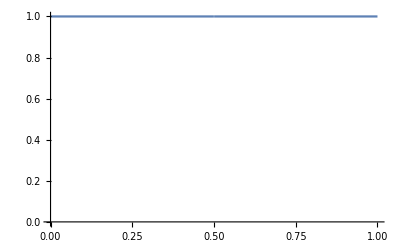

```mathematica
Plot[DifferentiableHardAND[b,0],{b,0,1},PlotRange->{{0,1},{0,1}},GridLines->{{1/2,1},{1/2,1}}]
```

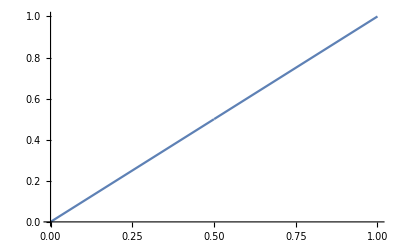

```mathematica
Plot[DifferentiableHardAND[b,1],{b,0,1},PlotRange->{{0,1},{0,1}},GridLines->{{1/2,1},{1/2,1}}]
```

```mathematica
Manipulate[Plot[DifferentiableHardAND[b,w],{b,0,1},PlotRange->{{0,1},{0,1}},GridLines->{{1/2,1},{1/2,1}}],{w,0,1}]
```

```mathematica
BooleanHardAND[b_,w_]:=b||!w
```

```mathematica
Manipulate[
GraphicsRow[{
Plot[DifferentiableHardAND[b,w],{b,0,1},PlotRange->{{0,1},{0,1}},GridLines->{{1/2,1},{1/2,1}},AxesLabel->Automatic],
DiscretePlot[Boole[BooleanHardAND[Harden[b],Harden[w]]],{b,0,1},PlotRange->{{0,1},{0,1}},ExtentSize->Full,Filling->Axis,AxesLabel->Automatic]
}],
{w,0,1}
]
```

```mathematica
Manipulate[
GraphicsRow[{
Plot[DifferentiableHardAND[b,w],{b,0,1},PlotRange->{{0,1},{0,1}},GridLines->{{1/2,1},{1/2,1}},AxesLabel->Automatic],
Plot[Evaluate[D[DifferentiableHardAND[b,w],b]],{b,0,1},PlotRange->{{0,1},{0,1}},GridLines->{{1/2,1},{1/2,1}},AxesLabel->Automatic]
}],
{w,0,1}
]
```

```mathematica
Manipulate[
GraphicsRow[{
Plot[DifferentiableHardAND[b,w],{w,0,1},PlotRange->{{0,1},{0,1}},GridLines->{{1/2,1},{1/2,1}},AxesLabel->Automatic],
Plot[Evaluate[D[DifferentiableHardAND[b,w],w]],{w,0,1},PlotRange->{{0,1},{0,-1}},GridLines->{{1/2,1},{1/2,1}},AxesLabel->Automatic]
}],
{b,0,1}
]
```

```mathematica
na=HardNeuralAND[2,4][[1]]
```

NetGraph[<>]

```mathematica
InitializeToConstant[na,0][{0.2,0.3}]
```

{0.982014,0.982014,0.982014,0.982014}

```mathematica
InitializeToConstant[na,1][{0.2,0.3}]
```

{0.0831727,0.0831727,0.0831727,0.0831727}

```mathematica
InitializeToConstant[na,1][{0.9,0.3}]
```

{0.167982,0.167982,0.167982,0.167982}

```mathematica
InitializeToConstant[na,1][{0.9,0.8}]
```

{0.916827,0.916827,0.916827,0.916827}

```mathematica
InitializeToConstant[na,1][{0.8,0.6}]
```

{0.689974,0.689974,0.689974,0.689974}